```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mgreen/GitHub Clones/rcDataLogger/CalibratePitot

```mathematica
data=Import["KODEE.TXT","Data"];
threadData=Dataset[Map[AssociationThread[First[data],#]&,Rest[data]]];
```

Dataset[<>]

```mathematica
airspeed=threadData[All,"Speed(MPH)"];
airspeed = airspeed[Select[#>16&]];
```

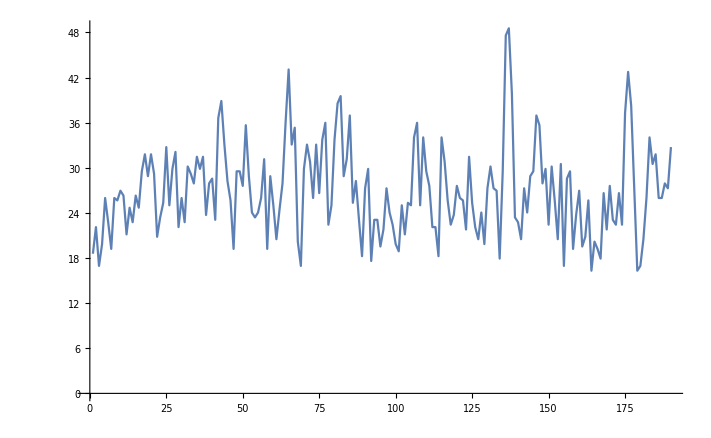

```mathematica
ListLinePlot[airspeed]
```